```mathematica
ClearAll["Global`*"]
```

```mathematica
Num=200;(*evaluate Num points*)
xStart=10;(*start at R=10Rb1*)
xEnd=38;(*end at R=38Rb1*)
xValues=Subdivide[xStart,xEnd,Num-1];(*separations to evaluate*)

NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"GMCalcLib_v2.0.nb"}]];
FilePath=FileNameJoin[{NotebookDirectory[],"data"}];(*path to the storage folder*)
```

```mathematica
GMMaxMChirp[q_,MBH_?NumericQ(*Ms as unit*),α_?NumericQ,Mcloud_(*M1 as unit*)]:=Module[
{SysEnergiesInLab,i,PInterpolation,EInterpolation,dEdR,diffEq,R0,sol,RInterpolation,FreqInterpolation,dFdR,dRdt,ChirpMassFunc,ChirpMassConst,tstop,func,maxResult,maxVal,tmax,targetVal,domainLeft,tLeft,fLeft,domainRight,tRight,fRight,width},GMInitialize[q,MBH,α,Mcloud,FilePath];
GetEigensystem[];
GetGRPower[];
GetCloudEnergiesInLab[];
SysEnergiesInLab[eigenvectorIndex_]:=Module[{ρ1Values,ρ2Values,Xsys,d1,d2,CurrentEnergiesInLab},ρ1Values=M2/(M1+M2)*xValues/. {M1->M,Q->q};
ρ2Values=M1/(M1+M2)*xValues/. {M1->M,Q->q};
Xsys=(Mc*Xcs[[eigenvectorIndex]]+M1*(-ρ1Values)+M2*ρ2Values)/(Mc+M1+M2)/. {M1->M,Q->q};
d1=M2/(M1+M2)*xValues+Xsys;(*CoM to BH1*)d2=M1/(M1+M2)*xValues-Xsys;(*CoM to BH2*)CurrentEnergiesInLab=Mc/μ*CloudEnergiesInLab[[All,eigenvectorIndex]]-(M1 M2)/(xValues Rb1)+1/2 M1 (π^2*GWFreqSquare[[eigenvectorIndex]]) (d1 Rb1)^2+1/2 M2 (π^2*GWFreqSquare[[eigenvectorIndex]]) (d2 Rb1)^2/. {M1->M,α1->α,Q->q}];

i=1;

(*interpolating functions*)
PInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},GRPower[[i]]}]];
EInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},SysEnergiesInLab[i]}]];
dEdR=Derivative[1][EInterpolation];

(*solve energy conservation equation*)
diffEq=dEdR[R[t]]*R'[t]/yrpl==-PInterpolation[R[t]];
R0=xValues[[Num-2]]/. {M1->M,α1->α,Q->q};
sol=NDSolve[{diffEq,R[0]==R0,WhenEvent[R[t]<=xValues[[2]]/. {M1->M,α1->α,Q->q},"StopIntegration"]},R,{t,0,Infinity}];
RInterpolation=R/. sol[[1]];

FreqInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},Sqrt[GWFreqSquare[[i]]]}]];
dFdR=Derivative[1][FreqInterpolation];
dRdt=Derivative[1][RInterpolation];

ChirpMassFunc=Function[t,(5/96 π^(-8/3)*FreqInterpolation[RInterpolation[t]]^(-11/3)*dFdR[RInterpolation[t]]*dRdt[t]/yrpl)^(3/5)/. {M1->M,α1->α,Q->q}];
ChirpMassConst=If[i<=3,((M1+Mc) M2)^(3/5)/(M1+M2+Mc)^(1/5)/. {M1->M,α1->α,Q->q},(M1 (M2+Mc))^(3/5)/(M1+M2+Mc)^(1/5)/. {M1->M,α1->α,Q->q}];
(*定义我们关心的函数*)
func[t_]:=ChirpMassFunc[t]/ChirpMassConst-1/. {M1->M,α1->α,Q->q};
tstop=dRdt["Domain"][[1,2]];

(*寻找最大值*)
maxResult=NMaximize[{func[t],0<t<=tstop},t,AccuracyGoal->3]
]

GMMchirpSummary[q_,MBH_?NumericQ(*Ms as unit*),α_?NumericQ,Mcloud_(*M1 as unit*),threshold_]:=Module[
{SysEnergiesInLab,i,PInterpolation,EInterpolation,dEdR,diffEq,R0,sol,RInterpolation,FreqInterpolation,dFdR,dRdt,ChirpMassFunc,ChirpMassConst,tstop,func,maxResult,maxVal,tmax,targetVal,domainLeft,tLeft,fLeft,domainRight,tRight,fRight,width},GMInitialize[q,MBH,α,Mcloud,FilePath];
GetEigensystem[];
GetGRPower[];
GetCloudEnergiesInLab[];
SysEnergiesInLab[eigenvectorIndex_]:=Module[{ρ1Values,ρ2Values,Xsys,d1,d2,CurrentEnergiesInLab},ρ1Values=M2/(M1+M2)*xValues/. {M1->M,Q->q};
ρ2Values=M1/(M1+M2)*xValues/. {M1->M,Q->q};
Xsys=(Mc*Xcs[[eigenvectorIndex]]+M1*(-ρ1Values)+M2*ρ2Values)/(Mc+M1+M2)/. {M1->M,Q->q};
d1=M2/(M1+M2)*xValues+Xsys;(*CoM to BH1*)d2=M1/(M1+M2)*xValues-Xsys;(*CoM to BH2*)CurrentEnergiesInLab=Mc/μ*CloudEnergiesInLab[[All,eigenvectorIndex]]-(M1 M2)/(xValues Rb1)+1/2 M1 (π^2*GWFreqSquare[[eigenvectorIndex]]) (d1 Rb1)^2+1/2 M2 (π^2*GWFreqSquare[[eigenvectorIndex]]) (d2 Rb1)^2/. {M1->M,α1->α,Q->q}];

i=1;

(*interpolating functions*)
PInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},GRPower[[i]]}]];
EInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},SysEnergiesInLab[i]}]];
dEdR=Derivative[1][EInterpolation];

(*solve energy conservation equation*)
diffEq=dEdR[R[t]]*R'[t]/yrpl==-PInterpolation[R[t]];
R0=xValues[[Num-2]]/. {M1->M,α1->α,Q->q};
sol=NDSolve[{diffEq,R[0]==R0,WhenEvent[R[t]<=xValues[[2]]/. {M1->M,α1->α,Q->q},"StopIntegration"]},R,{t,0,Infinity},AccuracyGoal->10,PrecisionGoal->15];
RInterpolation=R/. sol[[1]];

FreqInterpolation=Interpolation[Transpose[{xValues/. {M1->M,α1->α,Q->q},Sqrt[GWFreqSquare[[i]]]}]];
dFdR=Derivative[1][FreqInterpolation];
dRdt=Derivative[1][RInterpolation];

ChirpMassFunc=Function[t,(5/96 π^(-8/3)*FreqInterpolation[RInterpolation[t]]^(-11/3)*dFdR[RInterpolation[t]]*dRdt[t]/yrpl)^(3/5)/. {M1->M,α1->α,Q->q}];
ChirpMassConst=If[i<=3,((M1+Mc) M2)^(3/5)/(M1+M2+Mc)^(1/5)/. {M1->M,α1->α,Q->q},(M1 (M2+Mc))^(3/5)/(M1+M2+Mc)^(1/5)/. {M1->M,α1->α,Q->q}];
(*定义我们关心的函数*)
func[t_]:=ChirpMassFunc[t]/ChirpMassConst-1/. {M1->M,α1->α,Q->q};
tstop=dRdt["Domain"][[1,2]];

(*寻找最大值*)
maxResult=NMaximize[{func[t],0<t<=tstop},t,AccuracyGoal->3];
maxVal=maxResult[[1]];
tmax=t/. maxResult[[2,1]];
Rmax=RInterpolation[tmax];

(*定义目标值=最大值-threshold*)
targetVal=maxVal-threshold;

(*计算最大值的频率*)
fmax=FreqInterpolation[RInterpolation[tmax]];

(*查找左侧交点*)
domainLeft=0;
tLeft=domainLeft;
fLeft=FreqInterpolation[RInterpolation[domainLeft]];
If[func[domainLeft]<=targetVal,tLeft=t/. Quiet[FindRoot[func[t]==targetVal,{t,domainLeft,tmax},Method->"Brent",MaxIterations->100]];
fLeft=FreqInterpolation[RInterpolation[tLeft]];];

(*查找右侧交点*)
domainRight=tstop;
tRight=domainRight;
fRight=FreqInterpolation[RInterpolation[domainRight]];
If[func[domainRight]<=targetVal,tRight=t/. Quiet[FindRoot[func[t]==targetVal,{t,tmax,domainRight},Method->"Brent",MaxIterations->100]];
fRight=FreqInterpolation[RInterpolation[tRight]];];

(*计算宽度*)
width=tRight-tLeft;

(*Subscript[ω, nlm]*)
LevelFrequncy[n_,α1_]:=μ(1-α1^2/(2 n^2));
(*growth width*)
GrowthWidth[{n_,l_,m_},a_,M_,α1_]:=Module[{rplus,ΩH},
rplus=1+√(1-a^2);
ΩH=a/(2M rplus);(*This expression is wrong in paper Termination of Superradiance*)

2rplus (2^(4l+1)Factorial[n+l])/(n^(2l+4)Factorial[n-l-1])(Factorial[l]/(Factorial[2l]Factorial[2l+1]))^2 Product[k^2(1-a^2)+(a m-2rplus M LevelFrequncy[n,α1])^2,{k,1,l}] (m ΩH-LevelFrequncy[n,α1])α1^(4l+5)
];

a1=1;
a2=1;

(*a1=x/.NSolve[m1 x/(2M1(1+√(1-x^2)))-LevelFrequncy[n1,α1]==0/.{n1->2,m1->1}/.{α1->α,M1->M,Q->q},x][[1]];(*a1 when 211,1 stops to grow*)
a2=x/.NSolve[m2 x/(2M2(1+√(1-x^2)))-LevelFrequncy[n2,α2]==0/.{n2->2,m2->1}/.{α1->α,M1->M,Q->q},x][[1]];(*a2 when 211,1 stops to grow*)*)

ReducedHamiltonian=DimlessReducedHamiltonian*(μ α1^2)/.{α1->α,M1->M,Q->q};

(*reduced Hamiltonian with non-Hermiticity added*)
ReducedHamiltonianWithGrowthWidth=Map[
ReplacePart[#,{
{1,1}->#[[1,1]]+ⅈ GrowthWidth[{2,0,0},a1,M1,α1],
{2,2}->#[[2,2]]+ⅈ GrowthWidth[{2,1,-1},a1,M1,α1],
{3,3}->#[[3,3]]+ⅈ GrowthWidth[{2,1,1},a1,M1,α1],
{4,4}->#[[4,4]]+ⅈ GrowthWidth[{2,0,0},a2,M2,α2],
{5,5}->#[[5,5]]+ⅈ GrowthWidth[{2,1,-1},a2,M2,α2],
{6,6}->#[[6,6]]+ⅈ GrowthWidth[{2,1,1},a2,M2,α2]
}]/.{α1->α,M1->M,Q->q}&,
ReducedHamiltonian
];

(*find eigensystem*)
{eigenvaluesWithGrowthWidth,eigenvectorsWithGrowthWidth}=Transpose[Map[Eigensystem,ReducedHamiltonianWithGrowthWidth]];

EigenvaluesWithGrowthWidthDataRe=Transpose[{xValues,#}]&/@Transpose[Re[eigenvaluesWithGrowthWidth]];
EigenvaluesWithGrowthWidthDataIm=Transpose[{xValues,#}]&/@Transpose[Im[eigenvaluesWithGrowthWidth]];

EImInterpolation=Interpolation[EigenvaluesWithGrowthWidthDataIm[[i]]];
Growth=NIntegrate[EImInterpolation[RInterpolation[t]]*yrpl,{t,0,tmax}];

{tmax,maxVal,tLeft,tRight,width,fmax/Tpl,fLeft/Tpl,fRight/Tpl,Rmax,Growth}
]
```

```mathematica
c=299792458; (* the speed of light in astro. units *)
SnLISA[f_,NModel_,AModel_]:=20/3(4 SnAcc[f,NModel]+SnSn[f,AModel]+SnOmn[f])/L^2(1+(f/(0.41 c/(2L)))^2)/.{L->10^9(Boole[AModel=="A1"]+2Boole[AModel=="A2"]+5Boole[AModel=="A5"])};
SnAcc[f_,NModel_]:=9*10^-28 1/(2π f)^4(1+10^-4/f)Boole[NModel=="N1"]+9*10^-30 1/(2π f)^4(1+10^-4/f)Boole[NModel=="N2"];
SnSn[f_,AModel_]:=1.98*10^-23 Boole[AModel=="A1"]+2.22*10^-23 Boole[AModel=="A2"]+2.96*10^-23 Boole[AModel=="A5"];

SnOmn[f_]:=2.65*10^-23;

SnGal[f_,NModel_,AModel_]:=Piecewise[{
{(f)^-2.1*1.55206*10^-43,f≥10^-5&&f<5.3*10^-4},
{(f)^-3.235*2.9714*10^-47,f≥5.3*10^-4 &&f<2.2*10^-3},
{(f)^-4.85*1.517*10^-51,f≥2.2*10^-3&&f< 4*10^-3},
{(f)^-7.5*6.706*10^-58,f≥4*10^-3&&f<5.3*10^-3},
{(f)^-20*2.39835*10^-86,f≥5.3*10^-3&& f<10^-2}
}]Boole[AModel=="A1"]+Piecewise[{
{(f)^-2.3*10^-44.62,f≥10^-5&&f<10^-3},
{(f)^-4.4*10^-50.92,f≥10^-3&&f<10^-2.7},
{(f)^-8.8*10^-62.8,f≥10^-2.7&&f<10^-2.4},
{(f)^-20*10^-89.68,f≥10^-2.4&&f<10^-2}
}]Boole[AModel=="A5"]

SnLISAdefault[f_]:=SnLISA[f,"N2","A5"]+SnGal[f,"N2","A5"];

c0=299792458;(*m/s*)
G0=6.67*10^-11;(*N m^2/kg^2*)
H0=67.4*10^3;(*m/s/Mpc*)
Ωm=0.315;
ΩΛ=0.685;
Mpc=3.086*10^22;
DL[z_]:=Mpc/Lpl*(1+z)c0∫_0^z 1/(H0 √(Ωm(1+x)^3+ΩΛ))ⅆx;(*Natrual unit*)
```

```mathematica
SNRBBH[q_,M_,z_,DL_,fdetmin_,fdetmax_]:=Module[{Ms,Mchirp,hcBBH},
Ms=1.989*10^30;
Mchirp=q^(3/5)/(1+q)^(1/5)M*Ms;
hcBBH[fdet_]:=√(2/(π^2 DL^2)*π^(2/3)/(3 c0^3)((1+z)G0*Mchirp)^(5/3)(fdet)^(-1/3));
√NIntegrate[hcBBH[f]^2/(f*SnLISAdefault[f])*1/f,{f,fdetmin,fdetmax}]
]
SNRBBHRange[q_,M_(*Ms as unit 1*),z_,DL_(*SI*),Rmin_(*SI*),Tobs_(*yr as unit 1*),SnLISA_]:=Module[{Ms,yr,c0,G0,Mtot,Mchirp,hcBBH,SNRBBH,tc,fgwRdet,Tinit,fgwdetMax,fgwdetMin},
Ms=1.989*10^30;
yr=31536000;
c0=299792458;(*m/s*)
G0=6.67*10^-11;(*N m^2/kg^2*)
Mtot=(1+q)M*Ms;
Mchirp=q^(3/5)/(1+q)^(1/5)M*Ms;
fgwRdet[R_]:=1/(π(1+z))*√((G0*Mtot)/R^3);
hcBBH[fdet_]:=√(2/(π^2 DL^2)*π^(2/3)/(3 c0^3)((1+z)G0*Mchirp)^(5/3)(fdet)^(-1/3));
SNRBBH[fdetmin_,fdetmax_]:=√NIntegrate[hcBBH[f]^2/(f*SnLISA[f])*1/f,{f,fdetmin,fdetmax}];
tc[Mc_,fgw0_]:=(5 c0^5)/(256 fgw0^(8/3) (G0 Mc)^(5/3) π^(8/3));(*fgw0是source frame*)
fgwdetMax=fgwRdet[Rmin];
Tinit=tc[Mchirp,(1+z)fgwdetMax]+Tobs*yr;
fgwdetMin=((5 c0^5)/(256 Tinit (G0 Mchirp)^(5/3) π^(8/3)))^(3/8)/(1+z);
SNRBBH[fgwdetMin,fgwdetMax]
]
SNRBBHParam[q_,M_?NumericQ(*Ms as unit 1*),α_?NumericQ,z_,DL_(*SI*),Rmin_(*Rb1 as unit 1*),Tobs_(*yr as unit 1*),SnLISA_]:=Module[{Ms,c0,G0,Rb1},
Ms=1.989*10^30;
c0=299792458;(*m/s*)
G0=6.67*10^-11;(*N m^2/kg^2*)
Rb1=(G0*M*Ms)/(c0^2 α^2);
SNRBBHRange[q,M,z,DL,Rmin*Rb1,Tobs,SnLISA]
]
```

```mathematica
q=0.99;
z0=0.054;
CurrentDL=DL[z0];

(*(0.01,0.04,4)&(0.01,0.04,10)*)
CloudMass=0.1;
DetectThreshold=0.04;
DetectTime=10;(*yr*)

(*定义横纵坐标的范围*)
MRange=Range[10,100,1];  (*M0:10到100，步长1*)
alphaRange=Range[0.01,0.16,0.001];  (*α0:0.01到0.16，步长0.001*)
```

```mathematica
(*GMMaxMchirpResultsSamples=ParallelTable[Quiet[GMMchirpSummary[q,M0,α0,CloudMass,DetectThreshold]],{M0,MRange},{α0,alphaRange}];
Save[FileNameJoin[{FilePath,"GMMaxMchirpsamplesMc"<>ToString[CloudMass]<>".m"}],{GMMaxMchirpResultsSamples,CloudMass}];*)
```

```mathematica
(*SNRBBHsamples=ParallelTable[SNRBBHParam[q,M0,α0,z0,CurrentDL*Lpl,10,DetectTime,SnLISAdefault],{M0,MRange},{α0,alphaRange}];
Save[FileNameJoin[{FilePath,"SNRBBHsamplesAtTobs"<>ToString[DetectTime]<>".m"}],{SNRBBHsamples}];*)
```

```mathematica
(*SNRGMSamples=ParallelTable[SNRBBHParam[q,MRange[[i]],alphaRange[[j]],z0,CurrentDL*Lpl,GMMaxMchirpResultsSamples[[i,j]][[9]],DetectTime,SnLISAdefault],{i,1,Length[MRange]},{j,1,Length[alphaRange]}];
Save[FileNameJoin[{FilePath,"SNRGMsamplesAtTobs"<>ToString[DetectTime]<>".m"}],{SNRGMSamples}];*)
```

```mathematica
Get[FileNameJoin[{FilePath,"SNRGMsamplesAtTobs"<>ToString[DetectTime]<>".m"}]];
Get[FileNameJoin[{FilePath,"GMMaxMchirpsamplesMc"<>ToString[CloudMass]<>".m"}]];
```

```mathematica
Show[
ListContourPlot[Transpose[Map[If[#>=13,1,0]&,SNRGMSamples,{2}]],DataRange->{{First[MRange],Last[MRange]},{First[alphaRange],Last[alphaRange]}},Contours->{0.5},ContourStyle->Red,ContourShading->{None,Opacity[0.3,Red]}],ListContourPlot[Transpose[Map[If[#[[2]]>=DetectThreshold,1,0]&,GMMaxMchirpResultsSamples,{2}]],DataRange->{{First[MRange],Last[MRange]},{First[alphaRange],Last[alphaRange]}},Contours->{0.5},ContourStyle->Green,ContourShading->{None,Opacity[0.3,Green]}],
ListContourPlot[Transpose[Map[If[#[[5]]<=DetectTime,1,0]&,GMMaxMchirpResultsSamples,{2}]],DataRange->{{First[MRange],Last[MRange]},{First[alphaRange],Last[alphaRange]}},Contours->{0.5},ContourStyle->Blue,ContourShading->{None,Opacity[0.3,Blue]}],
Frame->True,FrameLabel->{"","α"},
GridLines->{None,{0.15}},GridLinesStyle->{Black,Dashed},
ImageSize->Large,LabelStyle->Directive[Black,FontSize->20]
]
```

-Graphics-

```mathematica
(*Plot[{GMMaxMChirp[0.99,40,0.1,pointsMc][[1]],GMMaxMChirp[0.5,40,0.1,pointsMc][[1]]},{pointsMc,0.001,0.01},PlotLegends->{"",""},AxesLabel->{"",""},ImageSize->Large,LabelStyle->Directive[Black,FontSize->20]]*)
```

# Individual Test

```mathematica
q=0.99;(*M2=QM1*)
MBH1=40;(*40 M_⊙, 1 M_⊙≈9.135*10^37 Subscript[M, pl]*)
α=0.01;(*fine structure constant*)
MCloud=0.1; (*total mass of the cloud*)
DetectThreshold=0.03;

Num=200;(*evaluate Num points*)
xStart=10;(*start at R=10Rb1*)
xEnd=38;(*end at R=38Rb1*)
xValues=Subdivide[xStart,xEnd,Num-1];(*separations to evaluate*)

NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"GMCalcLib_v1.2.nb"}]];

FilePath=FileNameJoin[{NotebookDirectory[],"data"}];(*path to the storage folder*)
GMInitialize[q,MBH1,α,MCloud,FilePath];
(*If you want to do numerical calculations...*)
(*Print["Computing integrands..."]
ComputeAndSaveIntegrands[]
Print["Computing Reduced Hamiltonian..."]
ComputeAndSaveReducedHamiltonian[]
Print["Computing Xc..."]
ComputeAndSaveXc[]
Print["Computing Qc..."]
ComputeAndSaveQc[]*)

MchirpResults=GMMchirpSummary[q,MBH1,α,MCloud,0.03];
SNRBBHParam[q,MBH1,α,z0,CurrentDL*Lpl,MchirpResults[[9]],MchirpResults[[5]],SnLISAdefault]
Print["Growth:",MchirpResults[[10]]]
```

NDSolve::evcvmit: 在 100 次迭代中，事件位置无法收敛到位于 t = 9.52913×10^8 和 t = 9.52923×10^8 之间的要求的准确度或者精度.

0.0106921

Growth:-175075.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 9.52913×10^8 and t = 9.52923×10^8.

1.14663

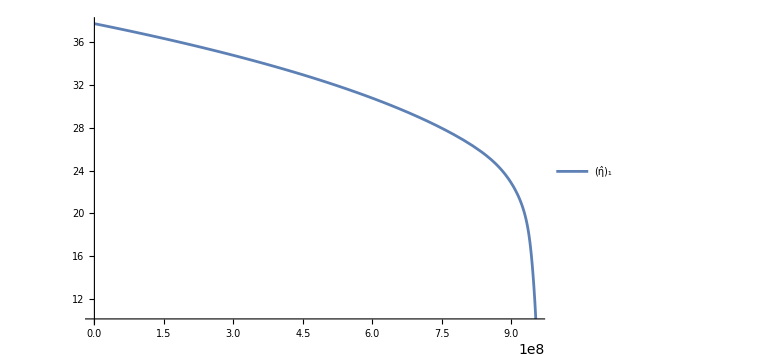

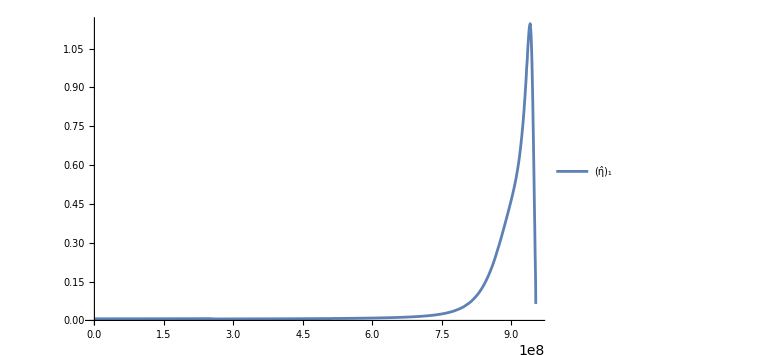

```mathematica
GetEigensystem[]
GetGRPower[]
GetCloudEnergiesInLab[]

SysEnergiesInLab[eigenvectorIndex_]:=Module[{ρ1Values,ρ2Values,Xsys,d1,d2,CurrentEnergiesInLab},
ρ1Values=M2/(M1+M2)*xValues/.{M1->M,Q->q};
ρ2Values=M1/(M1+M2)*xValues/.{M1->M,Q->q};
Xsys=(Mc*Xcs[[eigenvectorIndex]]+M1*(-ρ1Values)+M2*ρ2Values)/(Mc+M1+M2)/.{M1->M,Q->q};

d1=M2/(M1+M2)*xValues+Xsys;(*CoM to BH1*)
d2=M1/(M1+M2)*xValues-Xsys;(*CoM to BH2*)

CurrentEnergiesInLab=Mc/μ*CloudEnergiesInLab[[All,eigenvectorIndex]]-(M1 M2)/(xValues Rb1)+1/2 M1 (π^2*GWFreqSquare[[eigenvectorIndex]])(d1 Rb1)^2+1/2 M2(π^2*GWFreqSquare[[eigenvectorIndex]])(d2 Rb1)^2/.{M1->M,α1->α,Q->q}
]

RtPlots={};
ChirpMassPlots={};

For[i=1,i<=1,i++,

(*interpolating functions*)
PInterpolation=Interpolation[Transpose[{xValues/.{M1->M,α1->α,Q->q},GRPower[[i]]}]];
EInterpolation=Interpolation[Transpose[{xValues/.{M1->M,α1->α,Q->q},SysEnergiesInLab[i]}]];
dEdR=Derivative[1][EInterpolation];

(*solve energy conservation equation*)
diffEq=dEdR[R[t]]*R'[t]/yrpl==-PInterpolation[R[t]];
R0=xValues[[Num-2]]/.{M1->M,α1->α,Q->q};
sol=NDSolve[{diffEq,R[0]==R0,WhenEvent[R[t]<=xValues[[2]]/. {M1->M,α1->α,Q->q},"StopIntegration"]},R,{t,0,Infinity},AccuracyGoal->10,PrecisionGoal->15];
RInterpolation=R/. sol[[1]];

FreqInterpolation=Interpolation[Transpose[{xValues/.{M1->M,α1->α,Q->q},Sqrt[GWFreqSquare[[i]]]}]];
dFdR=Derivative[1][FreqInterpolation];
dRdt=Derivative[1][RInterpolation];
ChirpMassFunc=Function[t,(5/96 π^(-8/3)*FreqInterpolation[RInterpolation[t]]^(-11/3)*dFdR[RInterpolation[t]]*dRdt[t]/yrpl)^(3/5)/. {M1->M,α1->α,Q->q}];
ChirpMassConst=If[i<=3,((M1+Mc)M2)^(3/5)/(M1+M2+Mc)^(1/5)/.{M1->M,α1->α,Q->q},(M1(M2+Mc))^(3/5)/(M1+M2+Mc)^(1/5)/.{M1->M,α1->α,Q->q}];
(*plot*)
tstop=dRdt["Domain"][[1,2]];
AppendTo[RtPlots,Plot[RInterpolation[t],{t,0,tstop},PlotStyle->ColorData[97][i],PlotLegends->Placed[{ToExpression["\\hat{\\eta}_"<>ToString[i],TeXForm]},Right],PlotRange->All]];AppendTo[ChirpMassPlots,Plot[ChirpMassFunc[t]/ChirpMassConst-1/. {M1->M,α1->α,Q->q},{t,0,tstop},PlotStyle->ColorData[97][i],PlotLegends->Placed[{ToExpression["\\hat{\\eta}_"<>ToString[i],TeXForm]},Right],PlotRange->All]];
Print[NMaximize[{ChirpMassFunc[t]/ChirpMassConst-1,0<t<=tstop}/. {M1->M,α1->α,Q->q},t,AccuracyGoal->3][[1]]];
]

(*Origional1Rt[t_]:=(R0^4-256/5*(M1+Mc)M2(M1+M2+Mc)*t/Rb1^4)^(1/4)/.{M1->M,α1->α,Q->q};
Origional2Rt[t_]:=(R0^4-256/5*M1*(M2+Mc)(M1+M2+Mc)*t/Rb1^4)^(1/4)/.{M1->M,α1->α,Q->q};*)
Show[RtPlots,AxesLabel->{"",""},ImageSize->Large,LabelStyle->Directive[Black,FontSize->20],PlotRange->All]

AppendTo[ChirpMassPlots,Plot[MchirpResults[[2]]-DetectThreshold,{t,MchirpResults[[3]],MchirpResults[[4]]}]];
Show[ChirpMassPlots,AxesLabel->{"",""},ImageSize->Large,LabelStyle->Directive[Black,FontSize->20],PlotRange->All]
```

```mathematica
GRPower[[1,1]]
```

```mathematica
CurrentQBBH=M1*(M2/(M1+M2)*xValues*Rb1+(Mc*Xcs[[1]]*Rb1)/(M1+M2+Mc))^2+M2*(M1/(M1+M2)*xValues*Rb1-(Mc*Xcs[[1]]*Rb1)/(M1+M2+Mc))^2;

CurrentMassQuad=(Mc*Qcs[[i]]*Rb1^2+Table[SparseArray[{{1,1}->CurrentQBBH[[i]]},{3,3}],{i,1,Num}])/.{M1->M,α1->α,Q->q}; (*dimensionful*)
CurrentMassQuad
```

Part::partw: Part 7 of {{{{17.9917,2.96511×10^-17,0.},{2.96511×10^-17,8.80763,0.},{0.,0.,7.47087}},{{18.3387,3.74369×10^-19,0.},{3.74369×10^-19,8.82048,0.},{0.,0.,7.49537}},{{18.6991,-3.16846×10^-19,0.},{-3.16846×10^-19,8.83506,0.},{0.,0.,7.51867}},{{19.0727,8.74075×10^-20,0.},{8.74075×10^-20,8.85131,0.},{0.,0.,7.54085}},«43»,{{52.8154,-3.2573×10^-21,0.},{-3.2573×10^-21,10.2613,0.},{0.,0.,7.36186}},{{54.0842,-2.16319×10^-20,0.},{-2.16319×10^-20,10.2935,0.},{0.,0.,7.33389}},{{55.3793,-5.38717×10^-21,0.},{-5.38717×10^-21,10.3253,0.},{0.,0.,7.30523}},«150»},{«1»,«49»,«150»},{«1»},{«1»,«49»,«150»},{«1»},{{{20.379,4.57988×10^-18,0.},{4.57988×10^-18,19.2653,0.},{0.,0.,9.1593}},«49»,«150»}} does not exist.

real part of eigenvalues at a1=1, a2=1:

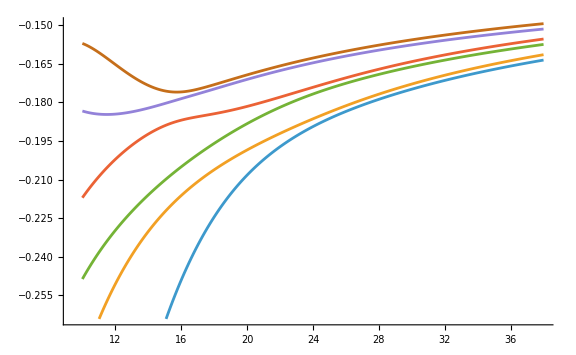

imaginary part (growth width) of eigenvalues at a1=1, a2=1:

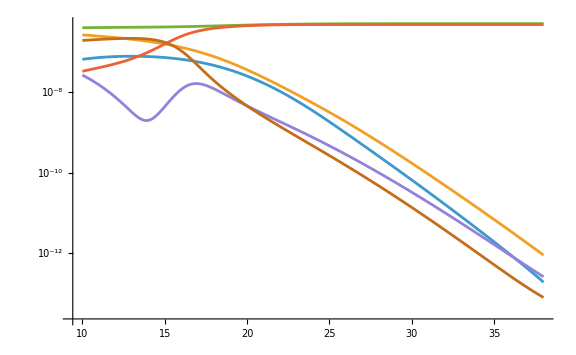

```mathematica
(*Subscript[ω, nlm]*)
LevelFrequncy[n_,α_]:=μ(1-α^2/(2 n^2));
(*growth width*)
GrowthWidth[{n_,l_,m_},a_,M_,α_]:=Module[{rplus,ΩH},
rplus=1+√(1-a^2);
ΩH=a/(2M rplus);(*This expression is wrong in paper Termination of Superradiance*)

2rplus (2^(4l+1)Factorial[n+l])/(n^(2l+4)Factorial[n-l-1])(Factorial[l]/(Factorial[2l]Factorial[2l+1]))^2 Product[k^2(1-a^2)+(a m-2rplus M LevelFrequncy[n,α])^2,{k,1,l}] (m ΩH-LevelFrequncy[n,α])α^(4l+5)
]

a1=1;
a2=1;

(*a1=x/.NSolve[m1 x/(2M1(1+√(1+x^2)))-LevelFrequncy[n1,α1]==0/.{n1->2,m1->1}/.{α1->α,M1->M,Q->q},x][[1]];(*a1 when 211,1 stops to grow*)
a2=x/.NSolve[m2 x/(2M2(1+√(1+x^2)))-LevelFrequncy[n2,α2]==0/.{n2->2,m2->1}/.{α1->α,M1->M,Q->q},x][[1]];(*a2 when 211,1 stops to grow*)*)

ReducedHamiltonian=DimlessReducedHamiltonian*(μ α1^2)/.{α1->α,M1->M,Q->q};

(*reduced Hamiltonian with non-Hermiticity added*)
ReducedHamiltonianWithGrowthWidth=Map[
ReplacePart[#,{
{1,1}->#[[1,1]]+ⅈ GrowthWidth[{2,0,0},a1,M1,α1],
{2,2}->#[[2,2]]+ⅈ GrowthWidth[{2,1,-1},a1,M1,α1],
{3,3}->#[[3,3]]+ⅈ GrowthWidth[{2,1,1},a1,M1,α1],
{4,4}->#[[4,4]]+ⅈ GrowthWidth[{2,0,0},a2,M2,α2],
{5,5}->#[[5,5]]+ⅈ GrowthWidth[{2,1,-1},a2,M2,α2],
{6,6}->#[[6,6]]+ⅈ GrowthWidth[{2,1,1},a2,M2,α2]
}]/.{α1->α,M1->M,Q->q}&,
ReducedHamiltonian
];

DimlessReducedHamiltonianWithGrowthWidth=ReducedHamiltonianWithGrowthWidth/(μ α1^2)/.{α1->α,M1->M,Q->q};
DimlessConjugateReducedHamiltonianWithGrowthWidth=Table[DimlessReducedHamiltonianWithGrowthWidth[[i]]†,{i,1,Num}];

(*find eigensystem*)
{DimlessREigenvaluesWithGrowthWidth,REigenvectorsWithGrowthWidth}=Transpose[Map[Eigensystem,DimlessReducedHamiltonianWithGrowthWidth]];
LEigenvectorsWithGrowthWidth=Table[REigenvectorsWithGrowthWidth[[i,j]]*/(REigenvectorsWithGrowthWidth[[i,j]]ᵀ.REigenvectorsWithGrowthWidth[[i,j]])*,{i,1,Num},{j,1,6}];(*LEigenvectorsWithGrowthWidth is *)

DimlessREigenvaluesWithGrowthWidthDataRe=Transpose[{xValues,#}]&/@Transpose[Re[DimlessREigenvaluesWithGrowthWidth]];
DimlessREigenvaluesWithGrowthWidthDataIm=Transpose[{xValues,#}]&/@Transpose[Im[DimlessREigenvaluesWithGrowthWidth]];

Print["real part of eigenvalues at a1=",a1,", a2=",a2,":"]
ListLinePlot[DimlessREigenvaluesWithGrowthWidthDataRe/.{α1->α,M1->M,Q->q},AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},LabelStyle->Directive[Black,FontSize->15]]

Print["imaginary part (growth width) of eigenvalues at a1=",a1,", a2=",a2,":"]
ListLinePlot[Abs[DimlessREigenvaluesWithGrowthWidthDataIm]/.{α1->α,M1->M,Q->q},AxesLabel->{"",""},ImageSize->Large,PlotLegends->{"","","","","",""},ScalingFunctions->{"Linear","Log10"},LabelStyle->Directive[Black,FontSize->15]]
```

```mathematica
LEigenvectorsWithGrowthWidth[[200,1]]†.REigenvectorsWithGrowthWidth[[200,1]]
```

1.-4.36289×10^-24 ⅈ

```mathematica
InitSet=<|"M"->40,"q"->0.99,"α"->0.1,"McOverM"->0.01,"a1"->1,"a2"->1,"R"->38|>
EvolveGM[DataSet_,NextR_]:=Module[{},]
```

```mathematica
1/(10^-4 μ α1^2)*Tpl/.{M1->M,α1->α}
```

2463.4

```mathematica
1/GrowthWidth[{2,0,0},1,10Ms,0.1]*Tpl/.{M1->M,α1->α}
```

-493.296

```mathematica
MassCompute[Separation_,eigenvector_]:=Module[{L,CloudField,MassIntegrand,TotalMass},
L=2Separation/.{α1->α,M1->M};
CloudField=HatStatesInCorotatingFrameNoDim.eigenvector;
MassIntegrand=Simplify[(CloudField * Conjugate[CloudField])/.{R->Separation}];
TotalMass=NIntegrate[MassIntegrand/.{α1->α,M1->M,Q->q},{x,-L,L},{y,-L,L},{z,-L,L},
PrecisionGoal->6,
AccuracyGoal->20,
MaxRecursion->40,
Method->{"LocalAdaptive"}]
]
MassCompute[xValues[[1]],eigenvectorsWithGrowthWidth[[100,1]]]
```

{1.25541}

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

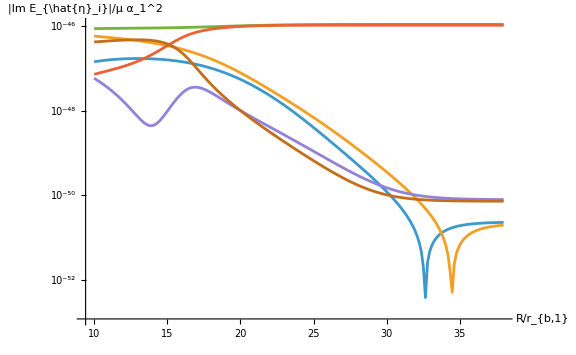

```mathematica
ListLinePlot[Abs[EigenvaluesWithGrowthWidthDataIm]/. {α1->α,M1->M,Q->q},AxesLabel->{"R/r_{b,1}","|Im E_{\hat{η}_i}|/μ α_1^2"},ImageSize->Large,ScalingFunctions->{"Linear","Log10"},LabelStyle->Directive[Black,FontSize->15],(*添加水平网格线*)GridLines->{None,(*x轴方向不添加网格线*)growthWidths[[All,2]]  (*y轴方向在指定值处添加网格线*)},GridLinesStyle->Directive[Gray,Dashed,Thickness[0.003]]]
```

```mathematica
eigenvectorsWithGrowthWidth[[1]]
```

{{0.258882+0.000790593 ⅈ,-0.0872214+0.0000493577 ⅈ,0.653816+0. ⅈ,0.25829+0.000745371 ⅈ,0.090983-0.0000512726 ⅈ,-0.65031-0.0000143099 ⅈ},{0.527691+0. ⅈ,-0.160071+0.00125532 ⅈ,-0.453921+0.00191663 ⅈ,-0.511091+0.000362755 ⅈ,-0.160808+0.0011496 ⅈ,-0.450324+0.00212967 ⅈ},{0.632982-0.000334618 ⅈ,0.216918-0.00101826 ⅈ,-0.218658-0.000650082 ⅈ,0.641141+0. ⅈ,-0.201874+0.00101396 ⅈ,0.229459+0.00102336 ⅈ},{0.175531-0.000149862 ⅈ,0.688616+0. ⅈ,-0.0292194+0.0013594 ⅈ,-0.191576+0.000244569 ⅈ,0.675515-0.000028104 ⅈ,-0.0334397+0.00139383 ⅈ},{0.172547-0.00107851 ⅈ,-0.662183-0.0000732243 ⅈ,-0.147323+0.000413058 ⅈ,0.156925-0.0011519 ⅈ,0.676557+0. ⅈ,0.166371-0.00017938 ⅈ},{0.439623-0.00195399 ⅈ,-0.083867-0.000374998 ⅈ,0.544157+0. ⅈ,-0.446853+0.00185494 ⅈ,-0.105142-0.000543345 ⅈ,0.541157-0.0000545401 ⅈ}}

```mathematica
eigenvectors[[200]]
```

{{-2.90155×10^-6,0.0134788,-0.999906,-0.000670676,-0.000258402,0.00246566},{-0.00136364,0.000278066,0.00247299,8.85869×10^-7,-0.01389,0.9999},{0.999996,-5.32218×10^-7,-1.33172×10^-6,0.00255208,0.000329508,0.00136835},{0.00255208,0.000704373,0.00068023,-0.999996,1.36752×10^-6,2.50717×10^-6},{6.29925×10^-7,-0.999909,-0.0134778,-0.000713476,0.000616042,0.000319961},{0.000348486,-0.000623391,0.000215746,-8.05189×10^-7,-0.999903,-0.01389}}

```mathematica
Sqrt[GWFreqSquare[[All,200]]]/(μ α^2)/. {α1->α,M1->M,Q->q}
```

{0.00196348,0.00196346,0.00196269,0.00196265,0.00196308,0.00196306}

```mathematica
GRPower[[All,200]]
```

{2.02011×10^-27,2.02416×10^-27,2.01623×10^-27,2.02017×10^-27,2.01748×10^-27,2.0215×10^-27}

```mathematica
CloudEnergiesInLab[[200]]/(μ α^2)/. {α1->α,M1->M,Q->q}
```

{-0.144631,-0.142277,-0.144572,-0.142216,-0.144622,-0.142267}

```mathematica
SysEnergiesInLab[eigenvectorIndex_]:=Module[{ρ1Values,ρ2Values,Xsys,d1,d2,CurrentEnergiesInLab},ρ1Values=M2/(M1+M2)*xValues/. {M1->M,Q->q};
ρ2Values=M1/(M1+M2)*xValues/. {M1->M,Q->q};
Xsys=(Mc*Xcs[[eigenvectorIndex]]+M1*(-ρ1Values)+M2*ρ2Values)/(Mc+M1+M2)/. {M1->M,Q->q};
d1=M2/(M1+M2)*xValues+Xsys;(*CoM to BH1*)d2=M1/(M1+M2)*xValues-Xsys;(*CoM to BH2*)CurrentEnergiesInLab=Mc/μ*CloudEnergiesInLab[[All,eigenvectorIndex]]-(M1 M2)/(xValues Rb1)+1/2 M1 (π^2*GWFreqSquare[[eigenvectorIndex]]) (d1 Rb1)^2+1/2 M2 (π^2*GWFreqSquare[[eigenvectorIndex]]) (d2 Rb1)^2/. {M1->M,α1->α,Q->q}];
SysEnergiesInLab[1][[200]]/. {α1->α,M1->M,Q->q}
```

-9.80526×10^33